```mathematica
tree16=EdgeAdd[PathGraph[Range[10]],{3<->11,11<->12,6<->13,13<->14,14<->15,9<->16}];
L=AdjacencyMatrix[tree16]-μ DiagonalMatrix[VertexDegree[tree16]];
L2=t IdentityMatrix[16]-L;
(*{P,T,Q}=ResourceFunction["PolynomialSmithDecomposition"][t IdentityMatrix[16]-L,t];*)
```

```mathematica
MatrixForm[L2,TableHeadings->{Range[16],Range[16]}]
```

( | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
1 | t+μ | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -1 | t+2 μ | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3 | 0 | -1 | t+3 μ | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
4 | 0 | 0 | -1 | t+2 μ | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5 | 0 | 0 | 0 | -1 | t+2 μ | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6 | 0 | 0 | 0 | 0 | -1 | t+3 μ | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
7 | 0 | 0 | 0 | 0 | 0 | -1 | t+2 μ | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
8 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | t+2 μ | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | t+3 μ | -1 | 0 | 0 | 0 | 0 | 0 | -1
10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | t+μ | 0 | 0 | 0 | 0 | 0 | 0
11 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t+2 μ | -1 | 0 | 0 | 0 | 0
12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | t+μ | 0 | 0 | 0 | 0
13 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | t+2 μ | -1 | 0 | 0
14 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | t+2 μ | -1 | 0
15 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | t+μ | 0
16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | t+μ)

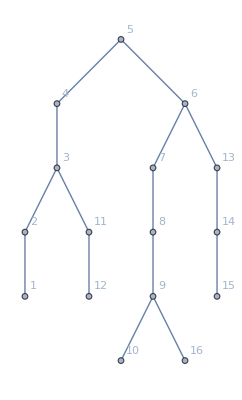

```mathematica
Graph[tree16,VertexLabels->Automatic]
```